## LE velocity (Ω)

```mathematica
f[x_,lp_]:=(2*x+(1/2)(1/(1-x))^2-1/2)/(2*lp)
k[k0_,x_,lp_,dR_]:=k0*Exp[-f[x,lp]*dR]
```

```mathematica
omega[k0_,x_,lp_,dR_]:=k[k0,x,lp,dR]*dR
```

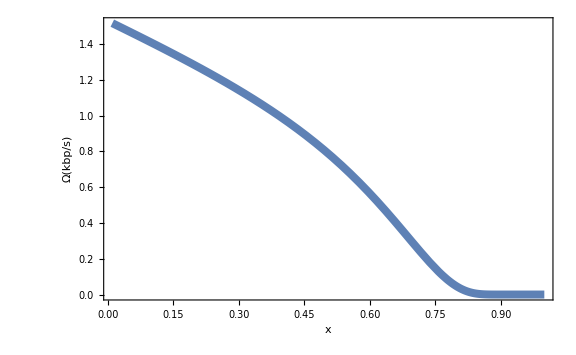

```mathematica
k0=20;dR=26;lp=50;(*parameters for the plot. Subscript[k, 0]=20(1/s), ΔR=26(nm), and persistence length 50(nm)*)
Plot[omega[k0,x,lp,dR]/0.34/1000 ,{x,0.01,1},PlotStyle->{Thickness[0.01]},Frame->True,Axes->False,FrameLabel->{{"Ω(kbp/s)",""},{"x",""}},LabelStyle->Directive[Black,20],FrameStyle->Directive[Black,20],TicksStyle->Directive[Black,20],ImageSize->Large,PlotRangeClipping->True]
```

## Ω with ATP dependence

```mathematica
kATP[T_,k0hat_,x_,lp_,dR_,KM_]:=(k0hat*T)/(KM+T)*Exp[-f[x,lp]*dR]
```

```mathematica
omegaATP[T_,k0hat_,x_,lp_,dR_,KM_]:=kATP[T,k0hat,x,lp,dR,KM]*dR
```

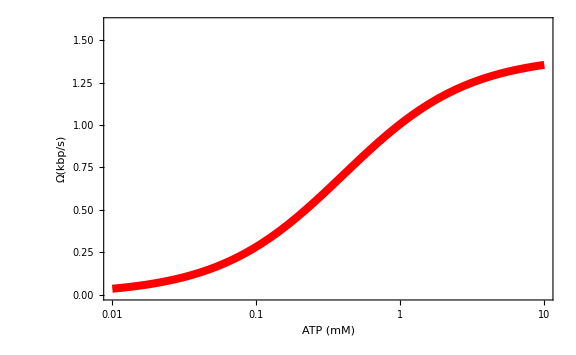

```mathematica
k0hat=20;lp=50;dR=26;x=0.1;KM=0.4;(*x is extension and KM is Michaelis-Menten constant*)
Show[LogLinearPlot[omegaATP[T,k0hat,x,lp,dR,KM]/0.34/1000 ,{T,0.01,10},PlotStyle->{Thickness[0.01],Red},PlotRange->{0,1.6}],Frame->True,Axes->False,FrameLabel->{{"Ω(kbp/s)",""},{"ATP (mM)",""}},LabelStyle->Directive[Black,20],FrameStyle->Directive[Black,20],TicksStyle->Directive[Black,20],ImageSize->Large,PlotRangeClipping->True]
```

## P(L|R)

```mathematica
t[L_,lp_]:=L/((2*lp)/3)
afa[L_,lp_]:=3*t[L,lp]/4
Nc[L_,lp_]:=(4*(afa[L,lp])^(3/2)Exp[afa[L,lp]])/(Pi^(3/2)*(4+12*(afa[L,lp])^-1+15(afa[L,lp])^-2))
PR[R_,L_,lp_]:=Nc[L,lp]*(4*Pi*(R/L)^2)/((1-(R/L)^2)^(9/2))Exp[(-3t[L,lp])/(4(1-(R/L)^2))]/L
PL[R_,L_,lp_]:=PR[R,L,lp]/NIntegrate[PR[R,LL,lp],{LL,R,Infinity}]
```

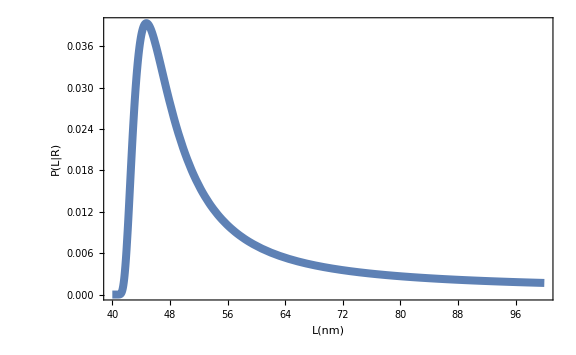

```mathematica
lp=50;R=40;
Plot[PL[R,L,lp],{L,40,100},PlotStyle->{Thickness[0.01]},Frame->True,Axes->False,FrameLabel->{{"P(L|R)",""},{"L(nm)",""}},LabelStyle->Directive[Black,20],FrameStyle->Directive[Black,20],TicksStyle->Directive[Black,20],ImageSize->Large,PlotRangeClipping->True]
```

## P(L|R,f)

```mathematica
PRfapp[f_,R_,L_,lp_,beta_]:=PR[R,L,lp]*Exp[beta*f*R]*Nc[L,lp]*Exp[-(1.0+3.3*Exp[-7*f])*f*L*beta]
PLfapp[f_,R_,L_,lp_,beta_]:=PRfapp[f,R,L,lp,beta]/NIntegrate[PRfapp[f,R,LL,lp,beta],{LL,R,Infinity}]
```

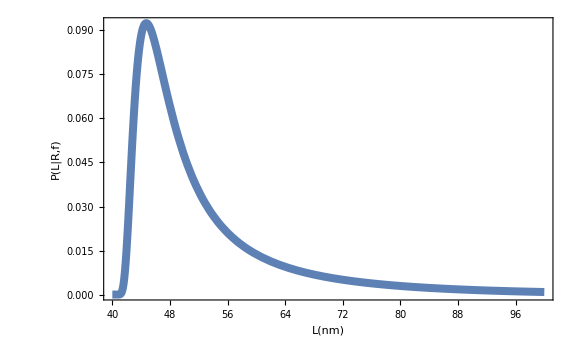

```mathematica
fex=0.2;lp=50;R=40;beta=1/4.1;(*fex is external load (pN) and beta is 1/Subscript[k, B]T*)
Plot[PLfapp[fex,R,L,lp,beta],{L,40,100},PlotRange->All,PlotStyle->{Thickness[0.01]},Frame->True,Axes->False,FrameLabel->{{"P(L|R,f)",""},{"L(nm)",""}},LabelStyle->Directive[Black,20],FrameStyle->Directive[Black,20],TicksStyle->Directive[Black,20],ImageSize->Large,PlotRangeClipping->True]
```

## P(ΔL)

```mathematica
Nrand=100;(*Number of the call for random number; 500 for the result in the main text (Calculation time is for a few hours for Nrand=500)*)
delx=0.2;(*bin size*)
std=13;(*Standart deviation for Gaussian random variavble*)
R1=40;(*Mean for Gaussian random variavble; initial size for condensin*)
R2=14;(*Size for condensin after conformational change*)
Lmax=170;(*Max length for the plot*)
```

```mathematica
distlistf0[L_,lp_]:=Table[PL[RandomVariate[NormalDistribution[R1,std],Nrand][[i]],L,lp],{i,Nrand}]
```

```mathematica
distlistposif0[L_,lp_]:=Cases[distlistf0[L,lp],s_/;Im[s]==0&&s>0]
```

```mathematica
sumLf0[L_,lp_]:=Total[distlistposif0[L,lp]]
```

```mathematica
tablesumLf0[lp_]:=Table[sumLf0[L,lp],{L,R2,Lmax,delx}]
```

```mathematica
listdistf0[lp_]:=Transpose@{Range[R2-R2,Lmax-R2,delx],tablesumLf0[lp]/(Total[tablesumLf0[lp]]*delx)}(*P(ΔL) for a given persistence length.*)
```

```mathematica
lp=42;(*Persistence length 42nm*)
PdL=listdistf0[lp];(*Calculation for P(ΔL). Calculation takes time so I recommend to save this output*)
```

```mathematica
PdLSmoothed=Transpose@{MovingAverage[PdL[[All,1]],50],MovingAverage[PdL[[All,2]],50]};(*Smooth the discrite distribution using box average*)
```

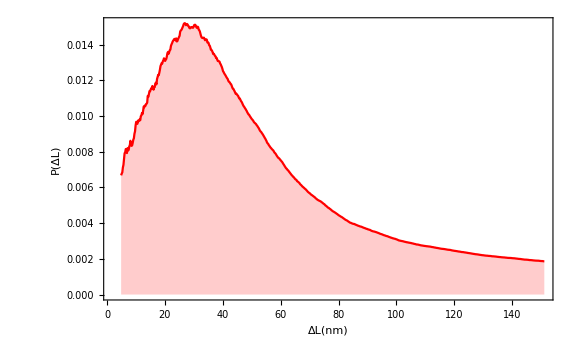

```mathematica
ListPlot[PdLSmoothed,PlotRange->All,Filling->Axis,FillingStyle->Automatic,PlotStyle->Red,Joined->True,Frame->True,Axes->False,FrameLabel->{{"P(ΔL)",""},{"ΔL(nm)",""}},LabelStyle->Directive[Black,20],FrameStyle->Directive[Black,20],TicksStyle->Directive[Black,20],ImageSize->Large,PlotRangeClipping->True](*Note that the plot is less smooth due to Nrand=100*)
```

## P(ΔL|f)

```mathematica
Nrand=100;(*Number of the call for random number; 500 for the result in the main text (Calculation time is for a few hours for Nrand=500)*)
delx=0.2;(*bin size*)
std=13;(*Standart deviation for Gaussian random variavble*)
R1=40;(*Mean for Gaussian random variavble; initial size for condensin*)
R2=14;(*Size for condensin after conformational change*)
Lmax=170;(*Max length for the plot*)
```

```mathematica
distlist[f_,L_,lp_]:=Table[PLfapp[f,RandomVariate[NormalDistribution[R1,std],Nrand][[i]],L,lp,1/4.1],{i,Nrand}]
```

```mathematica
distlistposi[f_,L_,lp_]:=Cases[distlist[f,L,lp],s_/;Im[s]==0&&s>0]
```

```mathematica
sumL[f_,L_,lp_]:=Total[distlistposi[f,L,lp]]
```

```mathematica
tablesumL[f_,lp_]:=Table[sumL[f,L,lp],{L,R2,Lmax,delx}]
```

```mathematica
listdist[f_,lp_]:=Transpose@{Range[R2-R2,Lmax-R2,delx],tablesumL[f,lp]/(Total[tablesumL[f,lp]]*delx)}(*P(ΔL|f) for a given persistence length.*)
```

```mathematica
lp=42;fex=0.1;(*Persistence length 42nm and external load 0.1pN*)
PdLf=listdist[fex,lp];(*Calculation for P(ΔL|f). Calculation takes time so I recommend to save this output*)
```

```mathematica
PdLfSmoothed=Transpose@{MovingAverage[PdLf[[All,1]],50],MovingAverage[PdL[[All,2]],50]};(*Smooth the discrite distribution using box average*)
```

```mathematica
ListPlot[PdLfSmoothed,PlotRange->All,Filling->Axis,FillingStyle->Automatic,PlotStyle->Red,Joined->True,Frame->True,Axes->False,FrameLabel->{{"P(ΔL)",""},{"ΔL(nm)",""}},LabelStyle->Directive[Black,20],FrameStyle->Directive[Black,20],TicksStyle->Directive[Black,20],ImageSize->Large,PlotRangeClipping->True](*Note that the plot is less smooth due to Nrand=100*)
```

-Graphics-